```mathematica
Needs["utilities`"]
Get[FileNameJoin@{NotebookDirectory[],"generalizedKlyshkoCriteria.m"}]

Qprobs[λs_,s_]:=poisson[λs,s]s!
```

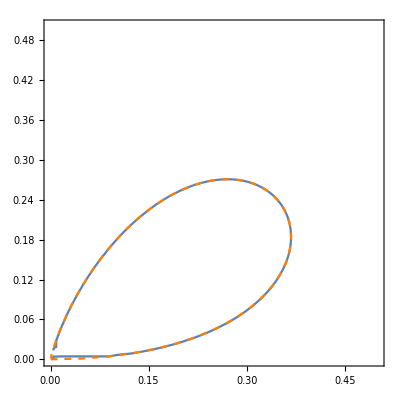

```mathematica
With[{q1=p1,q2=2p2},
Show[
ContourPlot[
p1+p2+q1^2/q2+q1^2/q2(Exp[q2/q1]-1-q2/q1-q2^2/(2 q1^2))==1,
{p1,0,.5},{p2,0,.5}],
ListPlot[
Table[poisson[μ,{1,2}],{μ,0,10,0.05}],
Joined->True,PlotStyle->{Dashed,Orange}
]
]
]
```

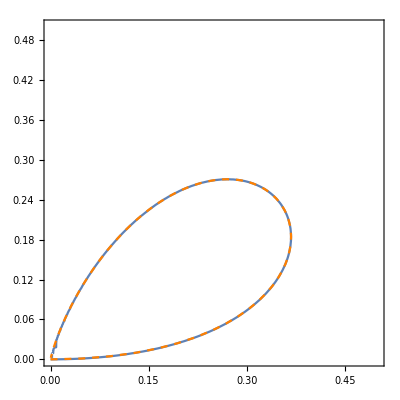

```mathematica
With[{q1=p1,q2=2p2},
Show[
ContourPlot[
q2==Exp[q2/q1] q1^2,
{p1,0,.5},{p2,0,.5}],
ListPlot[
Table[poisson[μ,{1,2}],{μ,0,10,0.05}],
Joined->True,PlotStyle->{Dashed,Orange}
]
]
]
```

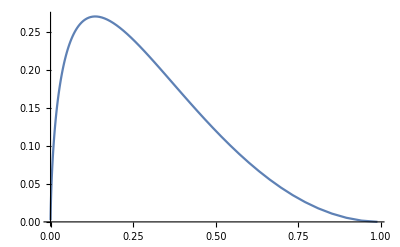

```mathematica
ListPlot[
Table[poisson[μ,{0,2}],{μ,0.01,10,0.05}],
Joined->True,PlotRange->All
]
```

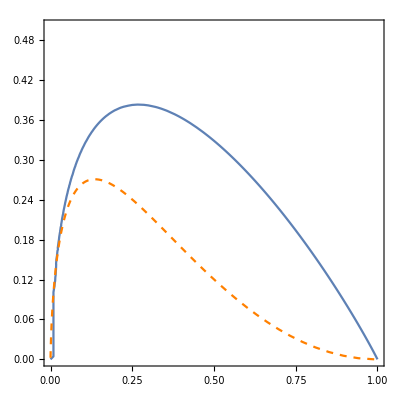

```mathematica
With[{q0=p0,q2=2p2},
Show[
ContourPlot[
p0+p2+q0(Exp[Sqrt[q2/q0]]-1-Sqrt[q2/q0]-q2/(2q0))==1,
{p0,0,1},{p2,0,.5}],
ListPlot[
Table[poisson[μ,{0,2}],{μ,0.01,10,0.05}],
Joined->True,PlotStyle->{Dashed,Orange}
]
]
]
```

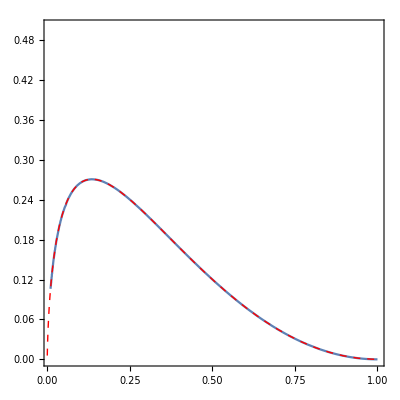

```mathematica
With[{q0=p0,q2=2p2},
Show[
ContourPlot[
{(*p0+(q2/q0)^(-3/2)+p2+q0(Exp[Sqrt[q2/q0]]-1-Sqrt[q2/q0]-q2/(2q0))==1,*)
q2==q0 (Log@q0)^2},
{p0,0.01,1},{p2,0,.5}],
ListPlot[
Table[poisson[μ,{0,2}],{μ,0.01,10,0.05}],
Joined->True,PlotStyle->{Dashed,Thin,Red}
]
]
]
```

```mathematica
Manipulate[
Show[
ContourPlot3D[
{q1 q2==q0 q3,
q1^2==q0 q2
},
{q0,0,1},{q1,0,ⅇ^-1},{q2,0,ⅇ^-2 2^2},
PlotRange->All,AxesLabel->{0,1,2},RotationAction->"Clip"],
ParametricPlot3D[ⅇ^-μ μ^{0,1,2},{μ,0,5},PlotStyle->Directive[Red,Dashed]]
],
{{q3,0.1},0,ⅇ^-3 3^3,Appearance->"Labeled"}
]
```

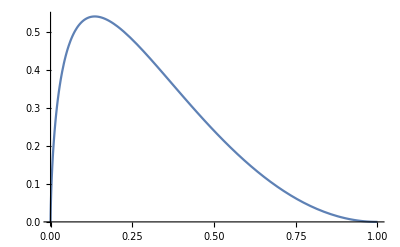

```mathematica
Plot[x(Log@x)^2,{x,0,1},PlotRange->All]
```

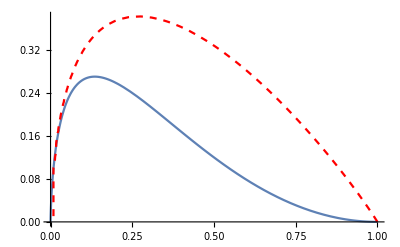

```mathematica
Show[
Plot[1/2x(Log@x)^2,{x,0,1},PlotRange->All],
ContourPlot[
p0+p2+p0(ⅇ^(√(2p2/p0))-1-√(2p2/p0)-p2/p0)==1,
{p0,0,1},{p2,0,1},ContourStyle->Directive[Dashed,Red]
]
]
```

```mathematica
Exp[x]+Exp[I x]+Exp[-I x]+Exp[-x]//FullSimplify
Exp[x]+I Exp[I x]-I Exp[-I x]-Exp[-x]//FullSimplify
```

2 (Cos[x]+Cosh[x])

-2 Sin[x]+2 Sinh[x]

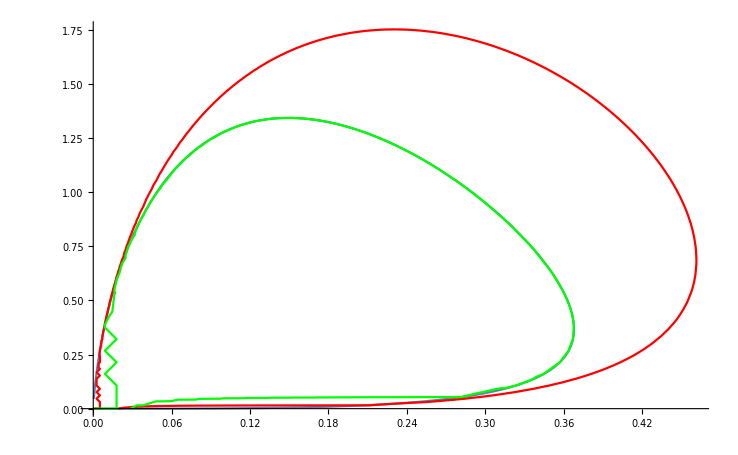

```mathematica
Show[
ParametricPlot[
ⅇ^-μ μ^{1,3},{μ,0,10},PlotRange->All,AspectRatio->1/GoldenRatio
],
ContourPlot[
√(q1^3/q3)Exp[√(q3/q1)]-(√(q1 q3))/2==1,{q1,0,1},{q3,0,6},ContourStyle->Red,PlotPoints->50
],
ContourPlot[
√(q1^3/q3)Exp[√(q3/q1)]==1,{q1,0,1},{q3,0,6},ContourStyle->Green
]
]
```